1. r^3

2.25859×10^29

Rstar=6.96342×10^8m

Rstarf=1.

Mstar=1.9884×10^30kg

m[Star]=m[1]kg

ρc=5.35863×10^14kg/(s^2 m)

1/Rp^2=4.42754×10^-30 1/m

Rs=2953.14m

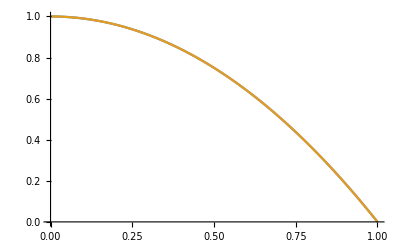

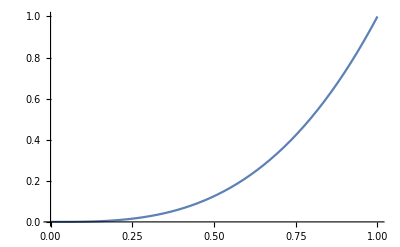

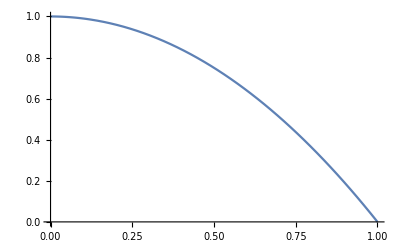

```mathematica
G:=6.67408*10^(-11)(*gravitational constant in SI units*)
c:=299792458(*speed of light in SI units*)
Msun:=1.9884*10^(30)(*mass of the sun in SI units*)
Rsun:=6.96342*10^8(*radius of the sun in SI units*)
Rstar:=1*Rsun(*radius of the star*)
Mstar:=1*Msun (*mass of the star*)
Rs:=2G*Mstar/(c^2)(*Schwarzschildradius*)
my0:=1*10^(-9)
ρ0:=3 Mstar/(4 π Rstar^3);
m[r]=4/3 π Rstar^3*r^3 ρ0/Mstar
Rp2=(Rs/Mstar ρ0(1-(1-2Rs/Rstar)^(1/2))/(3*(1-2Rs/Rstar)^(1/2)-1))^(-1)
pc:=1/Rp2*c^4/G
eqnP:={-p'[r]==Rstar*Rp2*(Rs*ρ0/Mstar+p[r]/(Rp2))*(Rs*m[r]+4*π*(Rstar*r)^3*p[r]/(Rp2))/((Rstar*r)^2-2*Rs*m[r]*(Rstar*r))}
condP:={p[my0]==1}
systemP:=Join[eqnP,condP]
state=First[NDSolve`ProcessEquations[systemP, {p}, {r, my0, 1}]];
NDSolve`Iterate[state,1]
sol=NDSolve`ProcessSolutions[state];
Rstarf=Last[state@"CurrentTime"[]];
Print["Rstar=",Rstar,"m"];
Print["Rstarf=",Rstarf,""];
Print["Mstar=",Mstar,"kg"];
Print["m[Star]=",m[1],"kg"];
Print["ρc=",1/Rp2*c^4/G,"kg/(s^2 m)"];
Print["1/Rp^2=",1/Rp2," 1/m"];
Print["Rs=",Rs,"m"];
pexakt[r]:=Rp2 *Rs/Mstar*ρ0((1-2Rs/Rstar)^(1/2)-(1-2Rs*r^2/(Rstar))^(1/2))/((1-2 Rs r^2 /Rstar)^(1/2)-3(1-2 Rs/Rstar)^(1/2))

Plot[{Evaluate[p[r]/.sol],Evaluate[pexakt[r]]},{r,my0,1}]
Plot[{Evaluate[m[r]]},{r,my0,1}]
Plot[{Evaluate[p[r]/.sol]},{r,my0,1}]
```